# Lecture 31: SVD Algorithms

Time to learn how to compute the SVD A=U.Σ.V^*.  Perhaps not surprisingly, SVD algorithms look quite a bit like eigenvalue algorithms.

## Eigenvalues of A^*.A

If A=U.Σ.V^* is the SVD then A^*.A=(U.Σ.V^*)^*.U.Σ.V^*=V.Σ^*.U^*.U.Σ.V^*=V.Σ^*.Σ.V^* since U is unitary.  More over, since Σ is real we wind up with A^*.A=V.Σ^2.V^*.  We can compute the Hermitian eigenvalue problem A^*.A=V.Λ.V^* then compute 
Σ as the diagonal matrix of the positive square roots of Λ and compute U from U.Σ=A.V.  The problem with this (or similarly computing with A.A^*) is that we know this problem (just like the normal equations) is more sensitive to perturbations than it needs to be.   The fundamental problem is the we formed the product. The stability problem is most extreme for the smaller singular values.

## Eigenvalues of H=(0 | A^* A | 0)

A direct computation shows that if A=U.Σ.V^* then 
	(0 | A^*
A | 0).(V | V
U | -U)=(A^*.U | -A^*.U
A.V | A.V)
Since A=U.Σ.V^* we have A.V=U.Σ.V^*.V=U.Σ.  
Since A^*=V.Σ.U^* we have that A^*.U=V.Σ.U^*.U=V.Σ. 
So
	(0 | A^*
A | 0).(V | V
U | -U)=(V.Σ | -V.Σ
U.Σ | U.Σ)=(V | V
U | -U).(Σ | 0
0 | -Σ).
In words, the eigen values of the big Hermitian matrix in the heading are the ± the singular values. The singular vectors are in the eigenvectors.

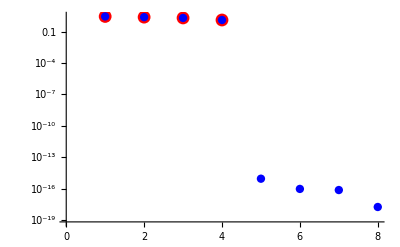

```mathematica
{m,n}={12,4};
A=RandomReal[{-1,1},{m,n}];
H=ArrayFlatten[({{0, ConjugateTranspose[A]}, {A, 0}})];
MatrixPlot[H];
{λ,V}=Eigensystem[H];
σ=SingularValueList[A];
ListLogPlot[{σ,Select[λ,Positive]},GridLines->Automatic,
PlotStyle->{Directive[Red,PointSize[0.023]],Directive[Blue, PointSize[0.015]]}]
```

This stable algorithm is what computes 99.999% of all SVDs in the world.  It is sneaky because it does not actualu need to make the big H matrix! Just like in eigenvalue land there is a preliminary reduction. In this case, we can get to a bi-diagonal matrix! The bi-idagonal form is then iteratively reduced to a diagonal form.

### Bi-diagonalization

The plan is to use Householder operations on the left and right to rotate the matrix to an upper bi-diagonal form.

```mathematica
{m,n}={10,4};
A=A0=RandomReal[{-1,1},{m,n}]
H
```

{{0.98716,0.445501,0.830686,-0.748829},{-0.477064,0.301204,0.384643,0.737181},{-0.0390946,0.244529,-0.243908,0.958791},{-0.529653,-0.441453,-0.185987,0.0453144},{-0.184185,-0.582139,-0.202184,0.771036},{0.779077,-0.0574551,0.215789,-0.897676},{-0.587475,-0.98797,0.57261,0.830203},{0.69388,0.885503,0.124528,-0.533651},{0.952075,-0.565976,-0.0442385,-0.787268},{-0.0861384,0.0288104,0.495201,-0.514302}}

## Backsubstitution: Function

```mathematica
BackSubstitution[R_,b_]:=Module[{x=0*R,m},
m=Length[R];
(* R is assumed to be square and lower triangular *)
Do[
x⟦j⟧=(b⟦j⟧-Sum[R⟦j,k⟧x⟦k⟧,{k,j+1,m}])/R⟦j,j⟧,
{j,m,1,-1}];
(* return x *)
x
]
```

Test.

```mathematica
m=6; 
R=UpperTriangularize[RandomReal[{-1,1},{m,m}]];
b=RandomReal[{-1,1},m];
LinearSolve[R,b]
BackSubstitution[R,b]
```

{-0.808741,-16.289,-8.65091,2.60397,-1.95016,0.20795}

{-0.808741,-16.289,-8.65091,2.60397,-1.95016,0.20795}

### Bad News abut Char Polys

Whatever